# FitzHugh-Nagumo model

#### Constant stimulation

```mathematica
constStimulation[a_, γ_, ϵ_, Iext_, tmin_, tmax_,minV_, maxV_, minw_, maxw_]:=Module[{eqV, eqw, eql, sys, vars, init, solution, 
timePlot, nullClines, vectorField, phasePlot, eqlPlot, aPlot},
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;
eql = NSolve[{eqV[V, w] == 0.0, eqw[V, w] == 0.0}, {V, w}, Reals];

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]};
vars = {V[t], w[t]};

init = Thread[{V[tmin], w[tmin]} == Values[eql][[1]] ];
solution = NDSolve[{sys, init}, vars, {t, tmin, tmax}];

timePlot = Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotStyle ->{Darker[Red],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large];

(* draw null clines *)
nullClines = ContourPlot[{eqV[V, w]== 0, eqw[V, w]== 0}, {V, minV, maxV}, {w, minw, maxw},
 Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1, ContourStyle -> {Orange, Darker[Green]}];
 (* draw vector field *)
vectorField = VectorPlot[{eqV[V, w], eqw[V, w] } , {V, minV, maxV}, {w,minw, maxw}, VectorStyle -> {Gray,"PinDart"}, VectorColorFunction->None, VectorPoints -> Fine];
phasePlot = ParametricPlot[Evaluate[vars/.solution], {t, tmin, tmax}, PlotStyle->Darker[Blue]];
(*equilibrium point*)
eqlPlot = ListPlot[{V, w} /. eql, PlotStyle -> {{Black, PointSize[0.02]}}, Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1];
(*threshold*)
aPlot = ListLinePlot[{{a, minw}, {a, maxw}}];

GraphicsRow[{Show[nullClines, vectorField, phasePlot, eqlPlot, aPlot], 
			timePlot}, ImageSize->Full]
]

Manipulate[constStimulation[a, γ, ϵ, Iext, tmin, tmax, Vmin, Vmax, wmin,wmax ], 
Style["Model parameters",12],
{{a,0.2,"a"},0.0,1,.01,Appearance-> "Labeled"},
{{γ,0.4,"γ"},0.0,1,.01,Appearance-> "Labeled"},
{{ϵ,0.001,"ϵ"},0.001,1,.01, Appearance-> "Labeled"},
{{Iext,0.3,Subscript[Style["I",Italic],"stim"]},0.0,1,.01, Appearance-> "Labeled"},
Delimiter,
{{tmin,0.0,Subscript[Style["t",Italic],"min"]},0,1000,1, Appearance-> "Labeled"},
{{tmax,20.0,Subscript[Style["t",Italic],"max"]},0,1000,1, Appearance-> "Labeled"},
{{Vmin,-0.5,Subscript[Style["V",Italic],"min"]},-1,1,.01, Appearance-> "Labeled"},
{{Vmax,1.5,Subscript[Style["V",Italic],"max"]},-1,1.5,.01, Appearance-> "Labeled"},
{{wmin,-0.5,Subscript[Style["w",Italic],"min"]},-1,1,.01, Appearance-> "Labeled"},
{{wmax,1.5,Subscript[Style["w",Italic],"max"]},-1,1.5,.01, Appearance-> "Labeled"}]
```

#### Periodic stimulation

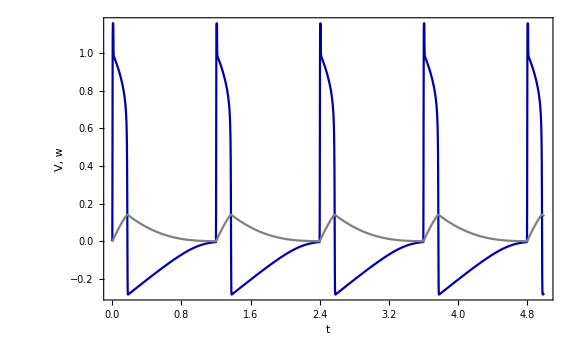

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)];
Iext = stimuliTrain[t, 0.2, 0.01, 1.2];
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext)
eqw[V_,w_]:=V-γ*w
pars={a->0.1,γ->0.5,ϵ->0.001};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 0.0;
tmax = 5;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, tmin, tmax}];
Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {All, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large]
```

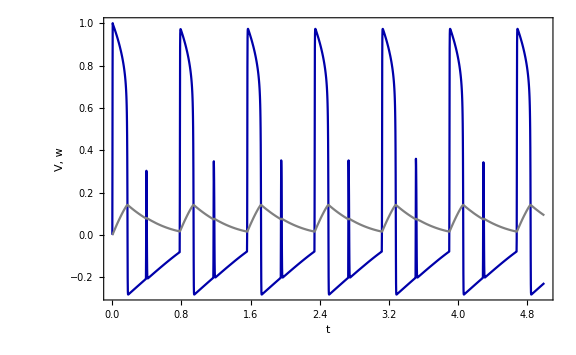

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)];
Iext = stimuliTrain[t, 0.2, 0.01, 0.39];
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext)
eqw[V_,w_]:=V-γ*w
pars={a->0.1,γ->0.5,ϵ->0.001};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 0;
tmax = 5;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, tmin, tmax}];
Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {All, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large]
```

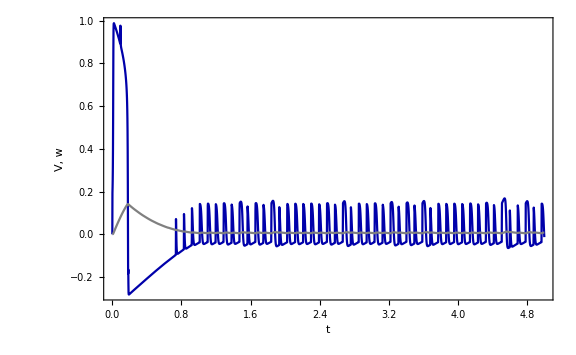

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)];
Iext = stimuliTrain[t, 0.2, 0.01, 0.092];
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext)
eqw[V_,w_]:=V-γ*w
pars={a->0.1,γ->0.5,ϵ->0.001};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 0;
tmax = 5;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, tmin, tmax}];
Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {All, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large]
```